```mathematica
(* функции взаимодействия с программой на C++ *)
ReadData[filename_] := Module[{data,T,E ,C ,M ,Mafm,MafmSum,χ,χafm,χafmvl,χafmhl,i,j, count,countJs,Js,dJs,NumberPar},
data=ReadList[filename,Word,WordSeparators->{";"}];
NumberPar=10;(*Количество наблюдаемых*)
countJs=ToExpression[data[[1]]];
Js=ToExpression[data[[2]]];
dJs=ToExpression[data[[3]]];
count = ((Length[data]-3)/countJs-1)/NumberPar; (* количество строк *)
E = Table[{},count*countJs];
M = Table[{},count*countJs];
Mafm = Table[{},count*countJs];
MafmSum = Table[{},count*countJs];
C = Table[{},count*countJs];
χ= Table[{},count*countJs];
χafm= Table[{},count*countJs];
χafmvl= Table[{},count*countJs];
χafmhl= Table[{},count*countJs];
For[j=0,j<countJs,j++,
For[i=0,i<count,i++,
T = ToExpression[data[[NumberPar*i+1+3+j+j*NumberPar*count+1]]];
E[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+2+3+j+j*NumberPar*count+1]]]};
M[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+3+3+j+j*NumberPar*count+1]]]};
Mafm[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+4+3+j+j*NumberPar*count+1]]]};
MafmSum[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+5+3+j+j*NumberPar*count+1]]]};
C[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+6+3+j+j*NumberPar*count+1]]]};
χ[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+7+3+j+j*NumberPar*count+1]]]};
χafm[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+8+3+j+j*NumberPar*count+1]]]};
χafmvl[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+9+3+j+j*NumberPar*count+1]]]};
χafmhl[[i+1+j*count]] = {T,ToExpression[data[[NumberPar*i+10+3+j+j*NumberPar*count+1]]]};
];
];
{E,M,Mafm,MafmSum,C,χ,χafm,χafmvl,χafmhl,countJs,Js,dJs,count}
]
```

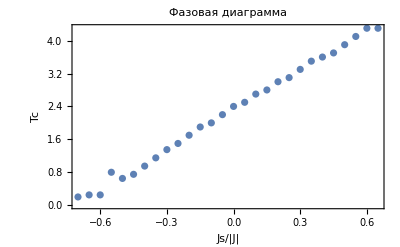

1.18238

1.18305

1.05501

1.3829

```mathematica
(* чтение результатов из тестового файла *)
filename = SystemDialogInput["FileOpen", NotebookDirectory[]];
{cppE,cppM,cppMafm,cppMafmSum,cppC,cppChi,cppChiafm,cppChiafmvl,cppChiafmhl,countJs,Js,dJs,count} = ReadData[filename];
cppEJ[j_]:=Table[cppE[[i+(j-1)*count]],{i,1,count}];
cppMJ[j_]:=Table[cppM[[i+(j-1)*count]],{i,1,count}];
cppMafmJ[j_]:=Table[cppMafm[[i+(j-1)*count]],{i,1,count}];
cppMafmSumJ[j_]:=Table[cppMafmSum[[i+(j-1)*count]],{i,1,count}];
cppCJ[j_]:=Table[cppC[[i+(j-1)*count]],{i,1,count}];
cppChiJ[j_]:=Table[cppChi[[i+(j-1)*count]],{i,1,count}];
cppChiafmJ[j_]:=Table[cppChiafm[[i+(j-1)*count]],{i,1,count}];
cppChiafmvlJ[j_]:=Table[cppChiafmvl[[i+(j-1)*count]],{i,1,count}];
cppChiafmhlJ[j_]:=Table[cppChiafmhl[[i+(j-1)*count]],{i,1,count}];
maxValue=Table[{},countJs];
For [p=1,p<=countJs,p++,
valueMaxC=Max[Table[cppCJ[p][[j]][[2]],{j,1,count}]];
For[k=1,k≤count,k++,
If[cppCJ[p][[k]][[2]]==valueMaxC,
maxValue[[p]]={Js+dJs*(p-1),cppCJ[p][[k]][[1]]};
];
];
];
ListPlot[maxValue,Frame->True,FrameLabel->{"Js/|J|","Tc"},PlotRange->All,PlotLabel->"Фазовая диаграмма"]


Manipulate[ListPlot[cppEJ[j],Frame->True,FrameLabel->{"T/J","E"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js+dJs*(j-1)])],{j,1,countJs,1}]
Manipulate[ListPlot[cppCJ[j],Frame->True,FrameLabel->{"T/J","C"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js+dJs*(j-1)])],{j,1,countJs,1}]
Manipulate[ListPlot[{cppMJ[j],cppMafmJ[j]},Frame->True,FrameLabel->{"T/J","M,Mafm"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js+dJs*(j-1)])],{j,1,countJs,1}]
Manipulate[ListPlot[cppMafmSumJ[j],Frame->True,FrameLabel->{"T/J","MafmSum"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js+dJs*(j-1)])],{j,1,countJs,1}]

Manipulate[ListPlot[cppChiJ[j],Frame->True,FrameLabel->{"T/J","χ"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js+dJs*(j-1)])],{j,1,countJs,1}]
Manipulate[ListPlot[cppChiafmJ[j],Frame->True,FrameLabel->{"T/J","χafm"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js+dJs*(j-1)])],{j,1,countJs,1}]
Manipulate[ListPlot[cppChiafmvlJ[j],Frame->True,FrameLabel->{"T/J","χafmvl"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js+dJs*(j-1)])],{j,1,countJs,1}]
Manipulate[ListPlot[cppChiafmhlJ[j],Frame->True,FrameLabel->{"T/J","χafmhl"},PlotRange->All,PlotLabel->(" Js = " <> ToString[Js+dJs*(j-1)])],{j,1,countJs,1}]
```

```mathematica
(* чтение нескольких файлов *)
files= SystemDialogInput["FileOpen", NotebookDirectory[]];
cppE = cppM = cppMafm = cppC = cppChi = cppChiafm = Table[0,Length[files]];
For[k = 1, k ≤Length[files],k++,
{cppE[[k]],cppM[[k]],cppMafm[[k]],cppC[[k]],cppChi[[k]],cppChiafm[[k]]} = ReadData[files[[k]]];
]
ListPlot[cppE,Frame->True,FrameLabel->{"T/J","E"},PlotRange->All]
ListPlot[cppM,Frame->True,FrameLabel->{"T/J","M"},PlotRange->All]
ListPlot[cppMafm,Frame->True,FrameLabel->{"T/J","Mafm"},PlotRange->All]
ListPlot[cppC,Frame->True,FrameLabel->{"T/J","C"},PlotRange->All]
ListPlot[cppChi,Frame->True,FrameLabel->{"T/J","χ"},PlotRange->All]
ListPlot[cppChiafm,Frame->True,FrameLabel->{"T/J","χ"},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»